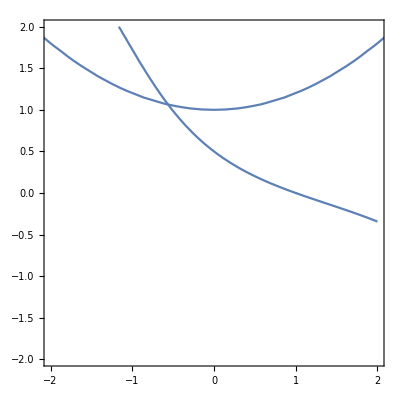

```mathematica
Show[{ContourPlot[x + 2 y + Sin[x]y ==1,{x,-2,2},{y,-2,2}],ContourPlot[-0.2 x^2 +y  ==1,{x,-4,4},{y,-4,4}]}]
```

```mathematica
FindRoot[{x + 2 y + Sin[x]y ==1,-0.2 x^2 +y  ==1},{x,-0.5},{y,1}]
```

{x→-0.560597,y→1.06285}

```mathematica
J={{D[x + 2 y + Sin[x]y,x],D[x + 2 y + Sin[x]y,y]},{D[-0.2 x^2 +y  ,x],D[-0.2 x^2 +y ,y]}}
```

{{1+y Cos[x],2+Sin[x]},{-0.4 x,1}}

```mathematica
J//MatrixForm
```

(1+y Cos[x] | 2+Sin[x]
-0.4 x | 1)

```mathematica
Simplify[Inverse[J].J]
```

{{1.,0.},{0.,1.}}

```mathematica
X0={0,0}
```

{0,0}

```mathematica
F[x_,y_]={x + 2 y + Sin[x]y -1,-0.2 x^2 +y  -1}
```

{-1+x+2 y+y Sin[x],-1-0.2 x^2+y}

```mathematica
NF[x_,y_] = {x,y}  -   F[x,y] . Transpose[Inverse[J]]
```

{x-((-1-0.2 x^2+y) (-2-Sin[x]))/(1+0.8 x+y Cos[x]+0.4 x Sin[x])-(-1+x+2 y+y Sin[x])/(1+0.8 x+y Cos[x]+0.4 x Sin[x]),y-((-1-0.2 x^2+y) (1+y Cos[x]))/(1+0.8 x+y Cos[x]+0.4 x Sin[x])-(0.4 x (-1+x+2 y+y Sin[x]))/(1+0.8 x+y Cos[x]+0.4 x Sin[x])}

```mathematica
X1=NF[0,0]
```

{-1.,1.}

```mathematica
X2=NF[X1[[1]],X1[[2]] ]
```

{-0.433772,0.973509}

```mathematica
X3=NF[X2[[1]],X2[[2]]]
```

{-0.561395,1.05978}

```mathematica
X4=NF[X3[[1]],X3[[2]]]
```

{-0.560595,1.06285}

```mathematica
TeXForm[{x + 2 y + Sin[x]y ==1,-0.2 x^2 +y  ==1}]
```

\left\{y \sin (x)+x+2 y=1,y-0.2 x^2=1\right\}

```mathematica
TeXForm[J]
```

\left(
\begin{array}{cc}
 y \cos (x)+1 & \sin (x)+2 \\
 -0.4 x & 1 \\
\end{array}
\right)